## Preamble

## Properties of Complex Numbers

### 0.) Preamble

```mathematica
z=1/2+1/2 √3 I;
w=-1/2+1/2 √3 I;
con=3;
w^6//Expand;
```

### 1)

```mathematica
Abs[z];
Abs[w];
Abs[z w];
Abs[z w]===Abs[z]Abs[w]
```

True

### 2)

```mathematica
Abs[w];
Abs[con w];
con Abs[w];
Abs[con w]===con Abs[w]
```

True

### demo)

```mathematica
Abs[ww]"1)"//TraditionalForm
"1)   "  Abs[ww]//TraditionalForm
```

1) Abs[ww]

1)    Abs[ww]

## Triangle Inequality Theorem

```mathematica
Abs[z+w]<=Abs[z]+Abs[w]
```

True

## Cauchy Riemann Equations

```mathematica
f[z_]:=z^3-z^2
ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}
```

-x^2+x^3+y^2-3 x y^2+ⅈ (-2 x y+3 x^2 y-y^3)

```mathematica
Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
```

-x^2+x^3+y^2-3 x y^2

-2 x y+3 x^2 y-y^3

```mathematica
D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]

D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]
-D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
```

-2 x+3 x^2-3 y^2

-2 x+3 x^2-3 y^2

2 y-6 x y

2 y-6 x y

## Length of a path

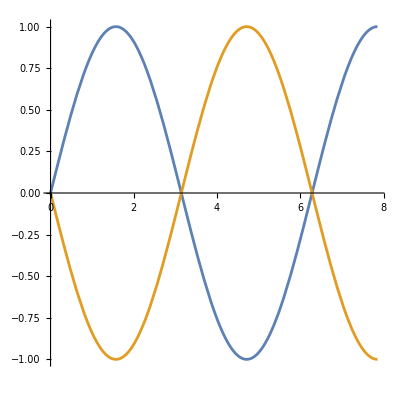

```mathematica
f[x_]:=Sin[x]
Plot[{f[x],Cos[x+Pi/2]},{x,0,2.5Pi},AspectRatio->1]
```

```mathematica
f'[t];
Integrate[√(1+f'[t]^2),{t,0,2Pi}];
Table[Integrate[√(1+Cos'[t-Pi/2]^2),{t,k/2 Pi,2Pi+k/2 Pi}],{k,0,2}]//TableForm
```

4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]

## tmp. notes

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
(1+I)^3/3//Simplify
```

-2/3+(2 ⅈ)/3

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{0,1},{1,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
CoordinateTransform["Polar"->"Cartesian",{r,θ}]
CoordinateTransform["Cartesian"-> "Polar",{x,y}]
CoordinateTransform["Cartesian"-> "Spherical",{x,y,0}]
```

{r Cos[θ],r Sin[θ]}

{√(x^2+y^2),ArcTan[x,y]}

{√(x^2+y^2),ArcTan[0,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
Conjugate[2+3I]
```

2-3 ⅈ

```mathematica
z=1+2I;
w=-1+√I;
Abs[z]Abs[w]//Simplify
Abs[z w]//Simplify
√3 Abs[z]
Abs[√3 z]
z/Abs[z]//Abs
w/Abs[w]//Abs
```

√(10-5 √2)

√(10-5 √2)

√15

√15

1

1

```mathematica
z/Abs[z]
Abs[z/Abs[z]]
```

(1+2 ⅈ)/(√5)

1

```mathematica
z Conjugate[z]
```

5

```mathematica
Abs[z]
Abs[Conjugate[z]]
```

√5

√5